# AdaptiveCellularAutomaton

One-line description explaining the function’s basic purpose

## Definition

```mathematica
ClearAll[TestCALifetime]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
TestCALifetime[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
colorrules = {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]};
```

```mathematica
toassoc[mufuncspec_]:= If[!MatchQ[mufuncspec, _Rule] && !MatchQ[mufuncspec, List[_Rule..]]&&!AssociationQ[mufuncspec],
 <|"MutatedRule"-> getmutationfunction[mufuncspec, "Rule"]|>,
Association[KeyValueMap[StringJoin["Mutated", #1]-> getmutationfunction[#2, #1]&,Association[mufuncspec]]]]
```

```mathematica
tofunction[mufuncassoc_]:=
Association[ 
KeyValueMap[
Function[{key, val},key->val[#]], mufuncassoc]]&
```

```mathematica
getmutationfunction[args_,"Rule"]:= 
Which[IntegerQ[args], RandomRuleMutation[#Rule, args]&,
ListQ[args], RandomRuleMutation[#Rule, First[args], Sequence@@Rest[args]]&,
True, args]
```

```mathematica
getmutationfunction[args_, "InitialCondition"]:= 
Which[IntegerQ[args], InitialConditionMutation[#InitialCondition, args]&,
ListQ[args], InitialConditionMutation[#InitialCondition, First[args], Sequence@@Rest[args]]&,
True, args]
```

```mathematica
ClearAll@getfitnessfunction
getfitnessfunction[evospec_]:= If[evospec["FitnessFunction"] === "Lifetime", TestCALifetime[CellularAutomaton[#1, #2, evospec["Cut"]]]&, evospec["FitnessFunction"]]
```

```mathematica
getsequence[evos_, seqspec_]:= 
If[seqspec=== "Breakthroughs",GatherBy[evos, #Fitness&][[All, 1]], evos]
```

```mathematica
ClearAll[getpropertyfunction]
getpropertyfunction[evospec_, prop_]:= Replace[prop,
{"Plot"->(ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#Rule, #InitialCondition, #Fitness + 1], ColorRules->colorrules, ImageSize->10Sqrt[#Fitness]]&),
Rule["Plot", stepspec_]:> 
(ArrayPlot[CellularAutomaton[#Rule, #InitialCondition, If[IntegerQ[stepspec] ||ListQ[stepspec], stepspec, stepspec[#]]], ColorRules->colorrules]&),
s_String:> (#[[s]]&),
l_List:> (#[[l]]&),
All:> (#[[All]]&),
o_:> o}
]
```

```mathematica
default = <|"Rule"->{0, 3, 1} , "InitialCondition"->{{1}, 0},"Cut"->100,"Depth"->100,
"MutationFunction"->(<|"Rule"->(RandomRuleMutation[#Rule]&)|>), "FitnessFunction"->"Lifetime", "SelectionFunction"->(#1>=#2&)|>;
```

```mathematica
ClearAll[AdaptiveCellularAutomaton]
AdaptiveCellularAutomaton[evospec_Association:default, sequencespec_String:"All", propertyspec_:{"Rule", "Fitness"}]:=Module[{},
merged = Join[default, evospec];
merged["MutationFunction"] = tofunction[toassoc[merged["MutationFunction"]]];
initialstate = 
<|"Rule"-> merged["Rule"],"InitialCondition"->merged["InitialCondition"],"MutatedRule"->merged["Rule"], 
"MutatedInitialCondition"->merged["InitialCondition"]|>;
fitnessfunction = getfitnessfunction[merged];
initialstate["Fitness"] = fitnessfunction[#Rule, #InitialCondition]&[initialstate];
initialstate["MutatedFitness"] = initialstate["Fitness"];
evos = 
If[sequencespec === "Final", Nest, NestList][
Block[{newstate = Join[#,merged["MutationFunction"][#]] },
newstate["MutatedFitness"] = fitnessfunction[#MutatedRule, #MutatedInitialCondition]&[newstate];
If[merged["SelectionFunction"][#MutatedFitness, #Fitness]&[newstate],newstate["Rule"] = newstate["MutatedRule"]; newstate["Fitness"] = newstate["MutatedFitness"]; newstate,
newstate]]&, initialstate, merged["Depth"]];
propertyfunction  = getpropertyfunction[merged,propertyspec];
If[sequencespec === "Final", propertyfunction@evos,propertyfunction/@ getsequence[evos, sequencespec]]]
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Run an evolution for 2 steps starting from the null k = 3, r = 1 rule:

```mathematica
AdaptiveCellularAutomaton[<|"Depth"->2|>]
```

{<|Rule→{0,3,1},Fitness→1|>,<|Rule→{354294,3,1},Fitness→1|>,<|Rule→{188286711948,3,1},Fitness→1|>}

Start from the k = 4, r = 1 rule:

```mathematica
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->2|>]
```

{<|Rule→{0,4,1},Fitness→1|>,<|Rule→{50331648,4,1},Fitness→1|>,<|Rule→{158456325028528675187138232320,4,1},Fitness→1|>}

```mathematica
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->2|>]
```

### Scope

Evolve for 500 steps and plot the breakthrough mutation steps :

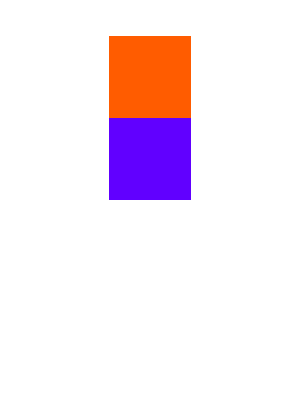
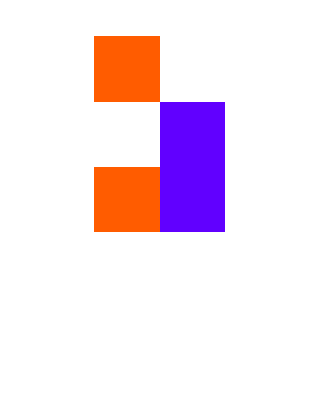
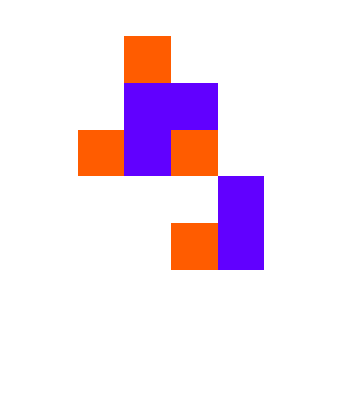
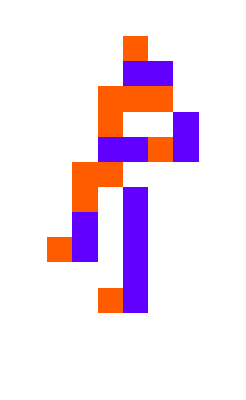
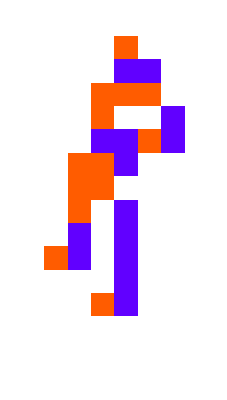
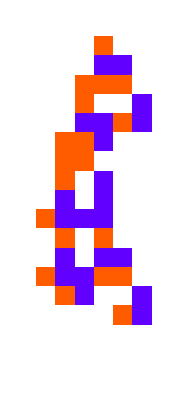
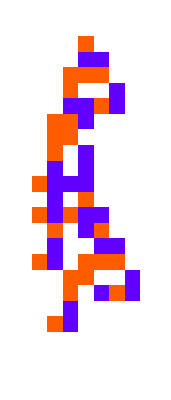
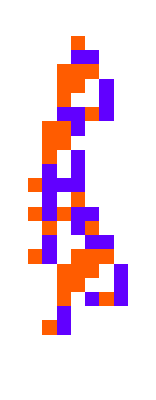
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[1110];AdaptiveCellularAutomaton[<|"Depth"->500|>, "Breakthroughs", "Plot"]
```

Plot the progressive fitness values showing the mutations that weren't selected:

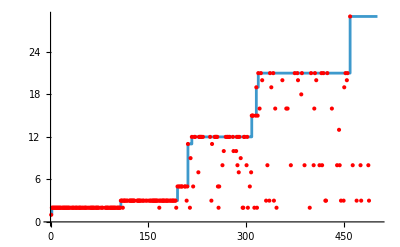

```mathematica
SeedRandom[1110];Show[ListStepPlot[#Fitness&/@ #], ListPlot[#MutatedFitness&/@ #, PlotStyle->Red]]&[AdaptiveCellularAutomaton[<|"Depth"->500|>, "All", {"Fitness", "MutatedFitness"}]]
```

Plot the progressive fitness values for 10 evolutions:

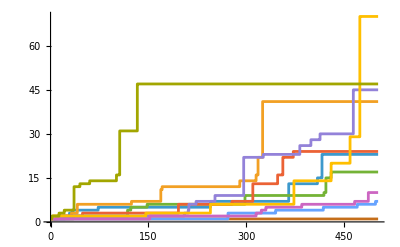

```mathematica
ListStepPlot[Table[AdaptiveCellularAutomaton[<|"Depth"->500|>, "All", "Fitness"], 10], PlotRange->All]
```

Plot the final states of 10 different evolutions:

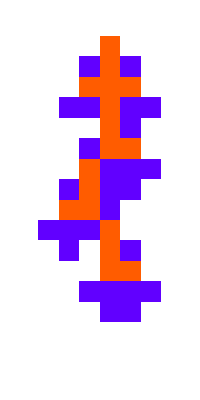
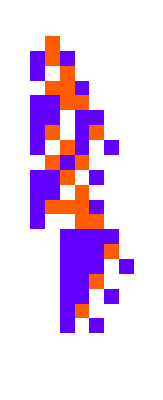
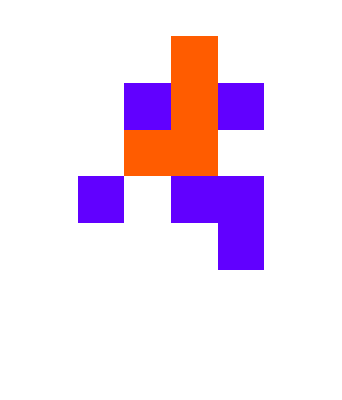
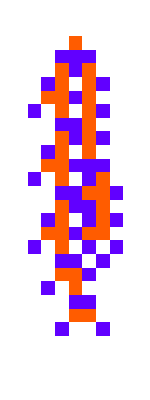
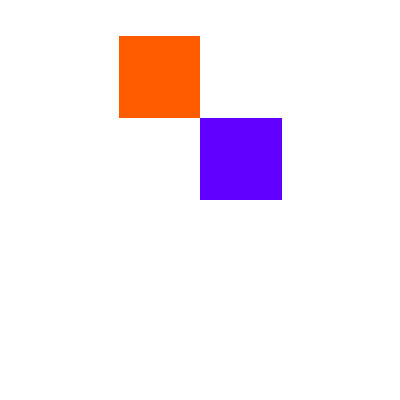
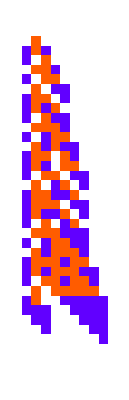
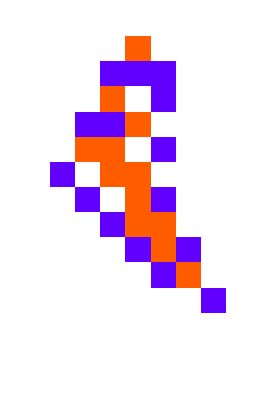
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[SeedRandom[1110+i];AdaptiveCellularAutomaton[<|"Depth"->500|>, "Final", "Plot"], {i, 10}]
```

Evolve a k = 4 cellular automata:

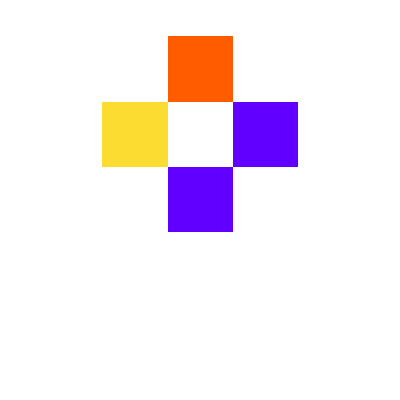
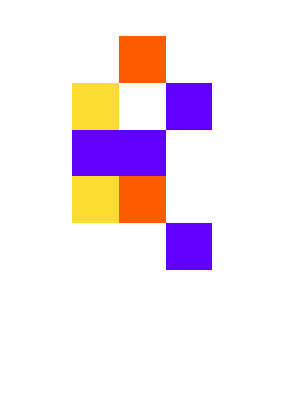
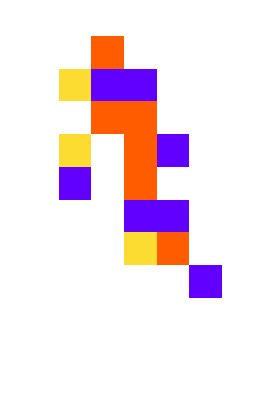
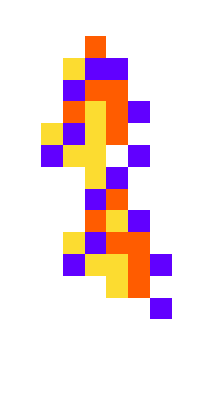
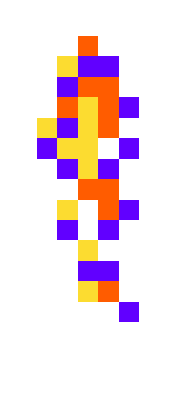
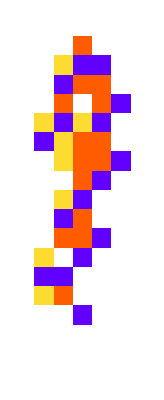
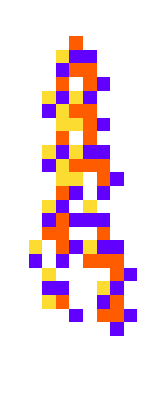
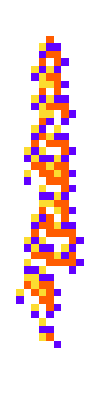
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[1112];AdaptiveCellularAutomaton[<|"Rule"-> {0, 4, 1},"Depth"->500|>, "Breakthroughs", "Plot"]
```

Plot with a length specification:

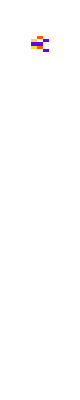
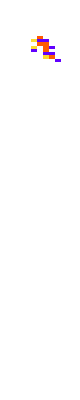
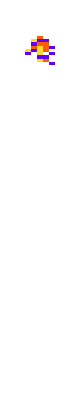
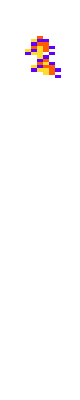
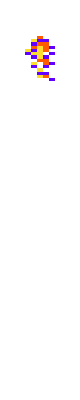
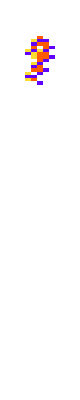
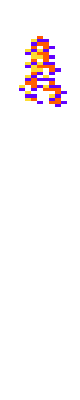
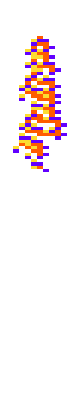
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[1112];AdaptiveCellularAutomaton[<|"Rule"-> {0, 4, 1},"Depth"->500|>, "Breakthroughs", "Plot"->{100, {-5, 5}}]
```

Manually adjust the output function:

```mathematica
SeedRandom[1112];AdaptiveCellularAutomaton[<|"Rule"-> {0, 4, 1},"Depth"->500|>, "Breakthroughs", (ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#Rule, #InitialCondition, #Fitness + 1], ColorRules->colorrules, ImageSize->30, Mesh->True, MeshStyle->Opacity[.15]]&)]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Search for longer automata:

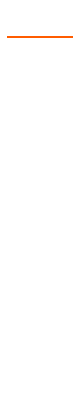
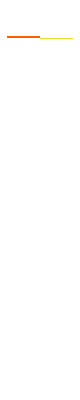
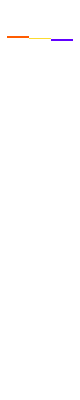
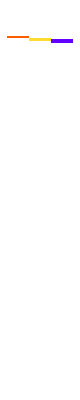
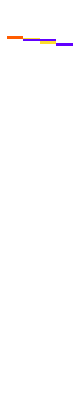
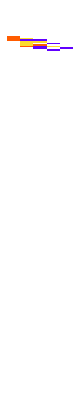
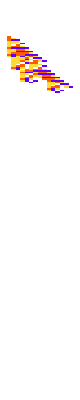
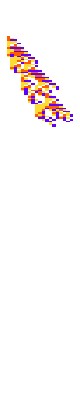

```mathematica
SeedRandom[1118];AdaptiveCellularAutomaton[<|"Rule"-> {0, 4, 1},"Depth"->500, "Cut"->200|>, "Breakthroughs", "Plot"->200]
```

```mathematica
AdaptiveCellularAutomaton[<|"Rule"-> {0, 4, 1},"Depth"->500|>, "Final"]
```

<|Rule→{42187832384047254621076511579181690760,4,1},Fitness→100|>

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.